```mathematica
(*Quit[]*)
```

```mathematica
(*

TODO

1. Update trapezoidal integration with something more accurate, e.g. Gauss integration (EM1985 used Simpson rule, but only in radial direction)
2. Update to handle n≠1 polytropic index.
3. Replace LegendereP with stable implementation.
4. Replace kernels with something free of Legendere expansion, e.g. EllipticK kernels
 


*)
```

```mathematica
totalTimer = AbsoluteTime[]
```

3.670845219093028×10^9

```mathematica
(*Import["http://adsabs.harvard.edu/abs/1985A%26A...146..260E","HTML"]; *)(* Uncomment line above to get main reference for the method. 
Eriguchi,Y.;Mueller,E., Astronomy and Astrophysics (ISSN 0004-6361),vol.146,no.2,May 1985,p.260-268.
*)
```

```mathematica
(* conv -> convert rationals onto machine precision numbers; if you prefer to keep rationals, use ,,identity'' conv *)
```

```mathematica
$OperatingSystem
```

Unix

```mathematica
$HomeDirectory
```

/home/misiek

```mathematica
dir=If[$OperatingSystem=="Windows","H:\\misiek/RotatingStars/EM/alphaEri/", "/home/misiek/RotatingStars/EM/alphaEri/"]
```

/home/misiek/RotatingStars/EM/alphaEri/

```mathematica
(*conv=(N[#]&)*)
```

```mathematica
conv=(# &)
```

#1&

```mathematica
NT=6(* angular rays (MAX NT=32 tested) *)
```

6

```mathematica
NR=6 (* radial slices, including surface, without center (MAX NR=32 tested ) *)
```

6

```mathematica
NL=6 (* number of Legendre polynomials (MAX NL=20 tested). WARNING: too large (e.g. NL=32) number of Legendere polynomials might cause numerical instability and catastrophic errors ! *)
```

6

```mathematica
R =Table[ToExpression["R"<>ToString[i]],{i,1,NT}](* radius of the stellar surface *)
```

{R1,R2,R3,R4,R5,R6}

```mathematica
r=Table[j/NR*R[[i]],{i,1,NT},{j,1,NR}]//conv; (* discretized radial grid coordinates *)
```

```mathematica
Δr=Table[If[j==NR,0,R[[i]]/NR],{i,1,NT},{j,1,NR}]//conv;
(* trapezoidal integration rule, central point not included, surface weigth assumed ZERO *)
```

```mathematica
θ=Table[Pi/2*i/(NT-1),{i,0,NT-1}]//conv;   (* angular grid *)
```

```mathematica
Δθ=Join[{Pi/2/(NT-1)/2},Table[Pi/2/(NT-1),{i,2,NT-1}],{Pi/2/(NT-1)/2}] //conv;(* trapezoidal rule *)
```

```mathematica
ρ=Table[
If[j==NR,0,ToExpression["ρ"<>ToString[i]<>"x"<>ToString[j]]
],{i,1,NT},{j,1,NR}] ;(* unknown densities at grid points; zero at surface *)
```

```mathematica
Ω=(Ω0&) (*solid body rotation *)
```

Ω0&

```mathematica
(*Ω=(Ω0/(1+#^2/A^2)&)*) (* j-const rotation law *)
```

```mathematica
(*-Integrate[ζ Ω[ζ]^2,{ζ,0,x}]*)
```

```mathematica
(*Refine[%,x>0&&A>0]*)
```

```mathematica
ΦC=-1/2 #^2 Ω0^2& (* solid body rotation *)
```

-1/2 #1^2 Ω0^2&

```mathematica
(*ΦC=A^2Ω0^2/2/(1+#^2/A^2)-1/2 A^2 Ω0^2& (* centrifugal potential; normalized to zero at center ! *)*)
```

```mathematica
ΦC[0]
```

0.

```mathematica
(*Limit[ΦC[x],x->Infinity]*)
```

```mathematica
kernel0[ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
If[ra≥rb,
Sum[
rb^(2n)/ra^(2n+1)
LegendreP[2 n, Cosθa]*LegendreP[2n ,Cosθb],
{n,0,nLeg}],
Sum[
ra^(2n)/rb^(2n+1)
LegendreP[2 n, Cosθa]*LegendreP[2n ,Cosθb],
{n,0,nLeg}]
]
```

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
DefaultCCompiler[]
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
$CCompiler
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
$CCompiler=DefaultCCompiler[]
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
part1=Sum[rb^(2n)/ra^(2n+1)
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part1NEW=part1//HornerForm;
```

```mathematica
part2=Sum[ra^(2n)/rb^(2n+1)
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2NEW=part2//HornerForm;
```

```mathematica
part1Da=Sum[D[rb^(2n)/ra^(2n+1),ra]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part1Db=Sum[D[rb^(2n)/ra^(2n+1),rb]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2Da=Sum[D[ra^(2n)/rb^(2n+1),ra]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2Db=Sum[D[ra^(2n)/rb^(2n+1),rb]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
kernel5=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1]//Evaluate,Evaluate[part2]]//Evaluate,CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->False}
]; (* this kernel seems to be fastest; tested on Microsoft Visual Studio Compiler and GCC *)
```

```mathematica
kernel5Da=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1Da],Evaluate[part2Da]]//Evaluate,CompilationTarget->"C"
]; (* derivatives of the kernel *)
```

```mathematica
kernel5Db=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1Db],Evaluate[part2Db]]//Evaluate,CompilationTarget->"C"
];
```

```mathematica
kernel[ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=kernel5[ra,Cosθa,rb,Cosθb]
(* wrapper for convenient use within Mathematica; note that this slow down by a factor of two *)
```

```mathematica
Derivative[1,0,0,0,0][kernel][ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
kernel5Da[ra,Cosθa,rb,Cosθb]
(* derivatives of the kernel required for Jacobian generation *)
```

```mathematica
Derivative[0,0,1,0,0][kernel][ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
kernel5Db[ra,Cosθa,rb,Cosθb]
```

```mathematica
vars=Join[Most[R],DeleteCases[Flatten[ρ],0],{C,ρC,K}]
```

{R1,R2,R3,R4,R5,ρ1x1,ρ1x2,ρ1x3,ρ1x4,ρ1x5,ρ2x1,ρ2x2,ρ2x3,ρ2x4,ρ2x5,ρ3x1,ρ3x2,ρ3x3,ρ3x4,ρ3x5,ρ4x1,ρ4x2,ρ4x3,ρ4x4,ρ4x5,ρ5x1,ρ5x2,ρ5x3,ρ5x4,ρ5x5,ρ6x1,ρ6x2,ρ6x3,ρ6x4,ρ6x5,C,ρC,K}

```mathematica
(* potencjal w centrum *)
```

```mathematica
Φ0=-4 Pi G Sum[Sin[θ[[l]]] Δθ[[l]] Sum[r[[l,m]]Δr[[l,m]] ρ[[l,m]],{m,1,NR}],{l,1,NT}];
(* gravitational potential at the center; NOTE: this is exact discretized formula, no Legendre expansion used *)
```

```mathematica
fLHS=
Function[Evaluate[vars],
Join[
{2 K ρC+ΦC[0]+Φ0-C},
{M-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
*ρ[[l,m]],
{l,1,NT},{m,1,NR}]},
Table[2 K ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]-4 Pi G Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
kernel[ r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]
*ρ[[l,m]],
{l,1,NT},{m,1,NR}]-C
,
{i,1,NT},{j,1,NR}
]
]//Flatten
(*,RuntimeAttributes->{Listable},Parallelization->True,
,CompilationOptions->{"ExpressionOptimization"->True}, CompilationTarget->"C"*)
];
```

```mathematica
Clear[G,M,K,ρC,ρ0]
```

```mathematica
Simplify[h[ζ]/2/K/.DSolve[{1/ζ^2D[ζ^2 h'[ζ],ζ]+4 Pi G /2/K h[ζ]==0,h[0]==2K ρ0,h'[0]==0},h[ζ],ζ][[1]]//ComplexExpand,K>0&&G>0](* initial values from Lane-Emden equation*)
```

(√(K/G) ρ0 Sin[√(G/K) √(2 π) ζ])/(√(2 π) ζ)

```mathematica
Simplify[%,G>0&&K>0]
```

(√(K/G) ρ0 Sin[√(G/K) √(2 π) ζ])/(√(2 π) ζ)

```mathematica
ρLE=Refine[%,G>0&&K>0]
```

(√(K/G) ρ0 Sin[√(G/K) √(2 π) ζ])/(√(2 π) ζ)

```mathematica
r0=Sqrt[K Pi/2/G]
```

√(K/G) √(π/2)

```mathematica
ρ0=ρ0/.Solve[M==Simplify[Integrate[4 Pi ζ^2 ρLE,{ζ,0,r0}],G>0&&K>0] (* MASS *),ρ0][[1]]
```

M/((K/G)^(3/2) √(2 π))

```mathematica
(*
Units tested:
1) K=1/2, G=1, ρ0=1
	2) G = 4 Pi^2, M=Msun, R=Rsun, Tsun = Keplerian period at R=Rsun 
*)
```

```mathematica
G0=6.67384*10^-11 (* From CODATA, used in Kong et. al. *)
```

6.67384×10^-11

```mathematica
(*G=1*)
```

```mathematica
G=4 Pi^2
```

4 π^2

```mathematica
(*G=G0*)
```

```mathematica
(*M=Sqrt[Pi]/2*)(* Lane-Emden with R=Sqrt[Pi]/2 radius and rhoC=1*)
```

```mathematica
QuantityMagnitude@Entity["Star","Sun"]["Mass"]
```

1.988435×10^30

```mathematica
Msun=1.98855*10^30 (* QuantityMagnitude@Entity["Star","Sun"]["Mass"]*)
```

1.98855×10^30

```mathematica
Rsun=695700000.0 (* QuantityMagnitude[Entity["Star","Sun"]["Radius"],"Meters"]*)
```

6.957×10^8

```mathematica
Tsun=2Pi Sqrt[Rsun^3/Msun/G0]
```

10008.2

```mathematica
M=9.7466*10^30/Msun (*α Eridani*)
```

4.90136

```mathematica
RαEri=8.83520*10^9
```

8.8352×10^9

```mathematica
RαEri/Rsun
```

12.6997

```mathematica
ΩαEri = 2.9725*10^-5
```

0.000029725

```mathematica
ΩαEri Tsun
```

0.297494

```mathematica
(*M=9.7466*10^30*)
```

```mathematica
K0=1.75*10^9  (* from Kong et. al. *)
```

1.75×10^9

```mathematica
Kinit=K0 Tsun^2 Msun/Rsun^5
```

2138.84

```mathematica
(*K=K0 Tsun^2 Msun/Rsun^5*)
```

```mathematica
(*K=K0*)
```

```mathematica
(*K=1/2*)
```

```mathematica
NT*NR+2 (* number of equations *)
```

38

```mathematica
Dimensions[vars] (* number of variables *)
```

{38}

```mathematica
(* init=RandomReal[1,NT*NR+2]*)
```

```mathematica
(* initial starting guess *)
```

```mathematica
init=Join[Most[R]/.(Rule[#,Sqrt[K Pi/2/G]]&)/@R,Flatten[Table[ρLE/.ζ->r[[i,j]]/.(Rule[#,Sqrt[K Pi/2/G]]&)/@R,{i,1,NT},{j,1,NR-1}],1],{-G M/r0,ρ0,K}]/.K->Kinit;
%//Short
```

{9.22506,9.22506,9.22506,«32»,-20.9753,0.00490342,2138.84}

```mathematica
start=Transpose[{vars,init}];
```

```mathematica
start[[-3;;]]
```

{{C,-20.9753},{ρC,0.00490342},{K,2138.84}}

```mathematica
Ω0=ΩαEri Tsun
```

0.297494

```mathematica
Evaluate[R⟦-1⟧]=RαEri/Rsun (* Thank Krzysztof Głód for this! *)
```

12.6997

```mathematica
wynik=Block[{s = 0, e = 0},{FindRoot[fLHS@@vars,start,MaxIterations->400,EvaluationMonitor:> e++, StepMonitor:> s++]//Chop//AbsoluteTiming,{s,e}}];
```

```mathematica
wynik//Short
```

{{1.51574,{R1→7.29891,R2→7.57877,«34»,ρC→0.00404111,K→1965.93}},{6,211}}

```mathematica
R⟦1⟧/R⟦-1⟧/.wynik⟦1,2⟧
```

0.57473

```mathematica
Sqrt[1-(R⟦1⟧/R⟦-1⟧)^2]/.wynik⟦1,2⟧
```

0.818343

```mathematica
{NT,NR,NL}
```

{6,6,6}

```mathematica
K/.wynik⟦1,2⟧
```

1965.93

```mathematica
Sqrt[1-0.745356^2] (* Kong et. al. *)
```

0.666667

```mathematica
Ωmax=0.37
```

0.37

```mathematica
ΔΩ=0.002
```

0.002

```mathematica
Ω
```

Ω0&

```mathematica
Clear[Ω0]
```

```mathematica
dir
```

/home/misiek/RotatingStars/EM/alphaEri/

```mathematica
For[Ω0=0.35,Ω0<=Ωmax,Ω0=Ω0+ΔΩ  ,
(*For[A=1.02,A>0,A=A-1/1000,*)
timer=AbsoluteTime[];
If[!FileExistsQ[dir<>"alphaEri_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_Omega_"<>ToString[N[Ω0]]<>".m"],
Block[{s = 0, e = 0},{rozw,evals}={FindRoot[fLHS@@vars,start,MaxIterations->128,EvaluationMonitor:> e++, StepMonitor:> s++]//Chop,{s,e}}];
Export[dir<>"alphaEri_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_Omega_"<>ToString[N[Ω0]]<>".m",rozw],
{rozw,evals}={Import[dir<>"alphaEri_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_Omega_"<>ToString[N[Ω0]]<>".m"],{"From disk",0,0}}
];
initPREV=vars/.rozw;
start=Transpose[{vars,initPREV}];
Print["Ω=",N[Ω0],"\t Time = ", AbsoluteTime[]-timer,"\n"];
Print["Evaluations=",evals[[2]],"\tStep=",evals[[1]] ,"\n"];
Print["b/a= ",R1/R⟦-1⟧/.rozw]
]
```

Ω=0.35	 Time = 0.006495

Evaluations=0	Step=From disk

b/a= 0.518268

Ω=0.352	 Time = 0.005747

Evaluations=0	Step=From disk

b/a= 0.516703

Ω=0.354	 Time = 0.005706

Evaluations=0	Step=From disk

b/a= 0.515196

Ω=0.356	 Time = 0.005719

Evaluations=0	Step=From disk

b/a= 0.513746

Ω=0.358	 Time = 0.005685

Evaluations=0	Step=From disk

b/a= 0.512352

Ω=0.36	 Time = 1.03272

Evaluations=141	Step=4

b/a= 0.511011

Ω=0.362	 Time = 1.04205

Evaluations=141	Step=4

b/a= 0.509724

Ω=0.364	 Time = 1.04769

Evaluations=141	Step=4

b/a= 0.508379

Ω=0.366	 Time = 1.03628

Evaluations=141	Step=4

b/a= 0.506938

Ω=0.368	 Time = 1.03281

Evaluations=141	Step=4

b/a= 0.505549

Ω=0.37	 Time = 1.0367

Evaluations=141	Step=4

b/a= 0.504211

```mathematica
Ωtest=0.34
```

0.34

```mathematica
Clear[dat]
```

```mathematica
dat[enum_]:=dat[enum]=Import[dir<>"alphaEri_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_Omega_"<>ToString[N[enum]]<>".m"]
```

```mathematica
dat[Ωtest]//Short
```

{R1→6.69477,R2→6.92008,R3→7.48707,«33»,ρC→0.00523613,K→1646.97}

```mathematica
Clear[powSpline]
```

```mathematica
Interpolation[Transpose[{θ,R}]/.rozw,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{0., 1.5708}}, <>]

```mathematica
powSpline[enum_]:=powSpline[enum]=Interpolation[Transpose[{θ,R}]/.Import[dir<>"alphaEri_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_Omega_"<>ToString[N[enum]]<>".m"],InterpolationOrder->3,Method->"Hermite"]
```

```mathematica
powSpline[Ωtest]
```

InterpolatingFunction[{{0., 1.5708}}, <>]

```mathematica
αEri=Interpolation[Transpose[{θ,R}]/.dat[Ωtest],InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{0., 1.5708}}, <>]

```mathematica
R[[1]]/R[[-1]]/.dat[Ωtest]
```

0.527158

```mathematica
R0=r0/.rozw
```

7.80494

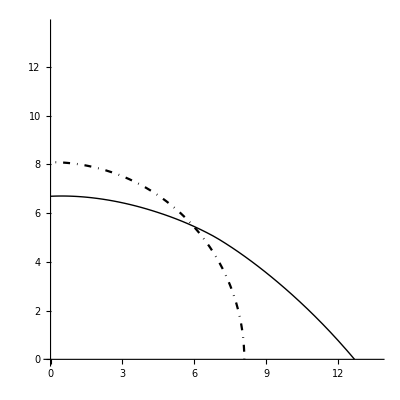

```mathematica
surf=PolarPlot[{αEri[Pi/2-θθ],(r0/.dat[Ωtest])},{θθ,0, Pi/2},AspectRatio->1,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,1.75 R0},{0,1.75R0}}]
```

```mathematica
R[[1]]/.rozw
```

6.50673

```mathematica
R[[-1]]
```

12.6997

```mathematica
%%/%
```

0.512352

```mathematica
K
```

K

```mathematica
SetOptions[PolarPlot,AspectRatio->2/3,PlotStyle->{{Medium,Black},{Dotted,Black,Medium}},PlotRange->R0{{-1.5,1.5},{-1.0,1.0}}];
```

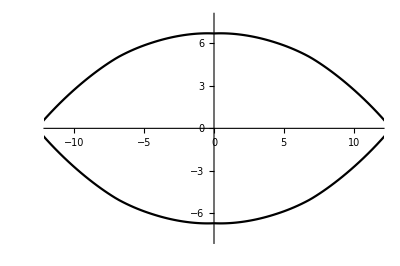

```mathematica
surfNEW=Show[PolarPlot[{powSpline[Ωtest][Pi/2-θθ],r0},{θθ,0, Pi/2}] ,PolarPlot[{powSpline[Ωtest][-Pi/2+θθ],r0},{θθ,Pi/2, Pi}] ,PolarPlot[{powSpline[Ωtest][-θθ+3Pi/2],r0},{θθ,Pi,3 Pi/2}] ,PolarPlot[{powSpline[Ωtest][-3/2Pi+θθ],r0},{θθ,3/2Pi, 2Pi}] ]
```

```mathematica
b=R[[1]]/.dat[Ωtest]
```

6.69477

```mathematica
a=R[[-1]]/.dat[Ωtest]
```

12.6997

```mathematica
b=2/3R[[-1]]/.rozw
```

8.46648

```mathematica
a=R[[-1]]/.rozw
```

12.6997

```mathematica
Ω0/.dat[Ωtest]
```

0.36

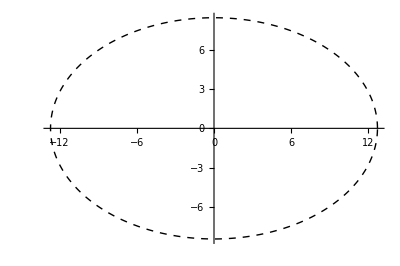

```mathematica
elipsa=ParametricPlot[{a Cos[t],b Sin[t]},{t,0,2Pi},PlotStyle->{{Thin,Dashed,Black}}]
```

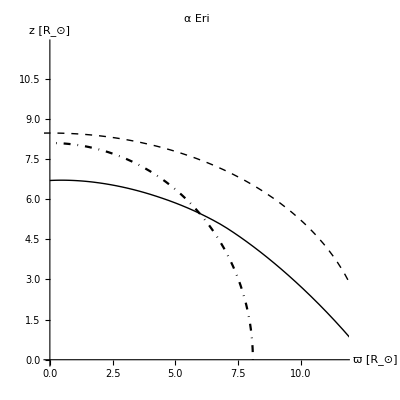

```mathematica
Show[surf,elipsa,AxesLabel->{"ϖ [R_⊙]","z [R_⊙]"},PlotLabel->"α Eri"]
```

```mathematica
Export[dir<>"Surface_alphaEri.pdf",%]
```

/home/misiek/RotatingStars/EM/alphaEri/Surface_alphaEri.pdf

```mathematica
Manipulate[
PolarPlot[{powSpline[i][Pi/2-θθ],(r0/.dat[i])},{θθ,0, Pi/2},AspectRatio->1/2,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,2.0},{0,1.0}}(r0/.dat[i]),
PlotLabel->"Re/Rp="<>ToString[R[[1]]/R[[-1]]/.dat[i]]<>
" C="<>ToString[C/.dat[i]]<>", K="<>ToString[K/.dat[i]]<>", Ω_0="<>ToString[i]
],{{i,Ωtest},0.0,Ωmax,ΔΩ}]
```

```mathematica
ρDISP=Flatten[Table[
If[j≠0,
{θ[[i]],r[[i,j]],ρ[[i,j]]},{θ[[i]],0,ρC}
]
,{i,1,NT},{j,0,NR}]/.dat[Ωtest],1]//Interpolation
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{0., 1.5708}, {0., 12.6997}}, <>]

```mathematica
ρDISPXY=ρDISP[θθ,rr]/.{rr->Sqrt[x^2+y^2],θθ->ArcTan[x/y]};
```

```mathematica
ρ0
```

485.027/K^(3/2)

InterpolatingFunction::dmval: Input value {1.56559,13.3801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.56819,13.3799} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

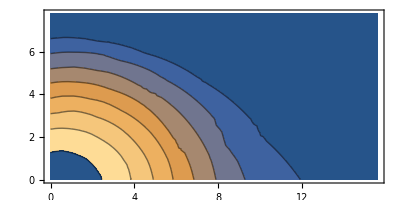

```mathematica
cp=ContourPlot[ρDISPXY*UnitStep[ρDISPXY],{x,0,2R0},{y,0,1R0},AspectRatio->1/2,PlotRange->All,Contours->(ρ0/.dat[Ωtest]){0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}]
```

General::prng: Value of option PlotRange -> {0,485.027/K^(3/2)} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

DensityPlot::prng: Value of option PlotRange -> {0,485.027/K^(3/2)} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

InterpolatingFunction::dmval: Input value {1.56923,12.7428} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.57002,12.7428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

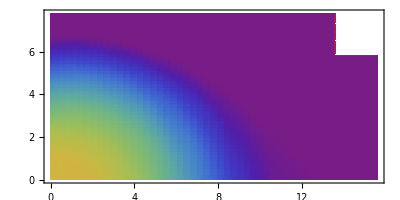

```mathematica
dp=DensityPlot[{ρDISPXY*UnitStep[ρDISPXY]+UnitStep[x-1.75R0]*UnitStep[y-0.75R0]},{x,0,2R0},{y,0,1R0},AspectRatio->1/2,PlotRange->{0,ρ0},ColorFunction->"Rainbow",PlotPoints->50]
```

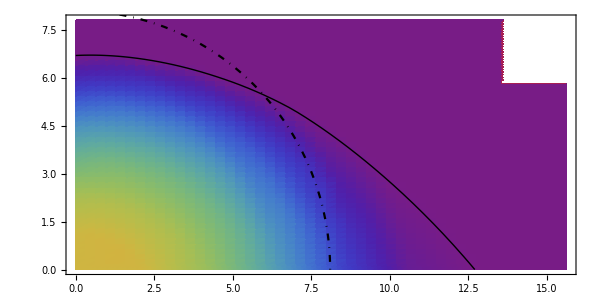

```mathematica
Show[dp,surf,ImageSize->600]
```

```mathematica
(*Export["H:\\misiek\\Articles\\SurfaceTracking\\figs\\j-const_A_02_J_02.png",%,ImageResolution->150]*)
```

```mathematica
Plot3D[ρDISPXY,{x,0,2.5r0},{y,0,2.5r0},AspectRatio->1,PlotRange->{0,All}]
```

Plot3D::plln: Limiting value 0.498678 √K in {x,0,2.5 r0} is not a machine-sized real number.

Plot3D[ρDISPXY,{x,0,2.5 r0},{y,0,2.5 r0},AspectRatio→1,PlotRange→{0,All}]

```mathematica
{{NT,NR,NL},{C,Ω0,R[[1]],R[[-1]]}}/.dat[Ωtest]
```

{{6,6,6},{-25.036,0.36,6.69477,12.6997}}

```mathematica
(*Table[{j,Ω0}/.dat[j],{j,0.0,Ωmax,ΔΩ}]*)
```

```mathematica
Rsun R[[-1]]/.rozw
```

8.8352×10^9

```mathematica
(*ListPlot[ Table[{j,Ω0}/.dat[j],{j,0.0,Ωmax,ΔΩ}],Joined->True]*)
```

```mathematica
R[[-1]]/.rozw
```

12.6997

```mathematica
(*ListPlot[ Table[{j,R[[1]]/R[[-1]]}/.dat[j],{j,0.0,Jmax,ΔJ}],Joined->True]*)
```

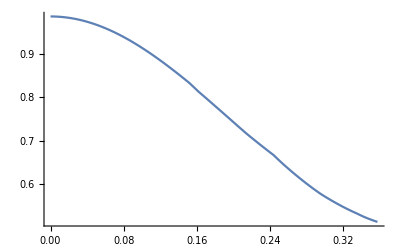

```mathematica
ListPlot[ Table[{j,R[[1]]/R[[-1]]}/.dat[j],{j,0.0,Ωmax-ΔΩ,ΔΩ}],Joined->True]
```

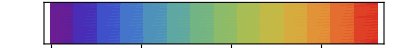

```mathematica
colorlabel=DensityPlot[x,{x,0,(ρ0/.dat[Ωtest])},{y,0,1/20},ColorFunction->"Rainbow",AspectRatio->1/20,Frame->True,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
Manipulate[
Show[
ListDensityPlot[{{{1.9,0.0,1},{2,1,1}},
Join[{{0,0,ρC}},
Flatten[
Table[
{
r[[i,j]]*Sin[θ[[i]]],
r[[i,j]]*Cos[θ[[i]]],
If[j==NR,0,ρ[[i,j]]
]
},{i,1,NT},{j,1,NR}]
,1]
]
/.dat[jj]
}
,AspectRatio->1/2,PlotRange->({{0,2r0},{0,1r0},{0,1ρ0}}/.dat[jj]),ColorFunction->"Rainbow",Mesh->False
]

,


Show@Table[ListPolarPlot[Table[{Pi/2-θ[[i]],r[[i,j]]},{i,1,NT}]/.dat[jj],Joined->True,InterpolationOrder->1,PlotStyle->{Thin,Black}],{j,1,NR}]
,
Show@Table[ListPolarPlot[{{0,0},{Pi/2-θ[[i]],r[[i,NR]]}}/.dat[jj],Joined->True,PlotStyle->{Thin,Black}],{i,1,NT}]
,
PolarPlot[{powSpline[jj][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2},AspectRatio->1,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,1.5},{0,1.5}}(r0/.dat[jj])

],
Frame->True,
FrameLabel->
"C="<>ToString[C/.dat[jj]]<>", ρ_c="<>ToString[ρC/.dat[jj]]<>", Ω_0="<>ToString[jj]
](*Show ends *)
,
{jj,0.0,Ωmax,ΔΩ}
]
```

```mathematica
ρC/.dat[0.1]
```

0.0020312

```mathematica
grid1=Show@Table[ListPolarPlot[Table[{Pi/2-θ[[i]],r[[i,j]]},{i,1,NT}]/.dat[Ωtest],Joined->True,InterpolationOrder->1,PlotStyle->{Thin,Black}],{j,1,NR}];
```

```mathematica
grid2=Show@Table[ListPolarPlot[{{0,0},{Pi/2-θ[[i]],r[[i,NR]]}}/.dat[Ωtest],Joined->True,PlotStyle->{Thin,Black}],{i,1,NT}];
```

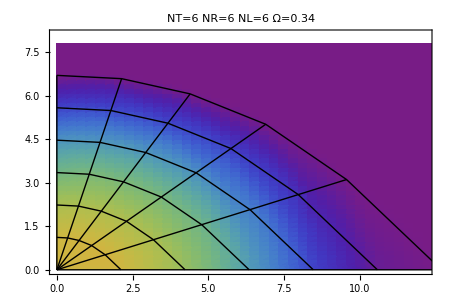

```mathematica
Show[dp,grid1,grid2,PlotLabel->"NT="<>ToString[NT]<>"\tNR="<>ToString[NR]<>"\tNL="<>ToString[NL]<>"\tΩ="<>ToString[Ωtest],ImageSize->450,PlotRange->{{0,1.5},{0,1}}(r0/.dat[Ωtest]),AspectRatio->2/3]
```

```mathematica
R/.dat[Ωtest]
```

{6.69477,6.92008,7.48707,8.52438,10.0565,12.6997}